## 2D Chain-Lattice

### Model

```mathematica
(*Define a function to generate the coordinates of a 2D tight-binding square lattice*)squareLatticeCoordinates[length_,width_,ax_,ay_]:=Module[{coordinates},coordinates=Table[{i*ax,j*ay},{i,0,length-1},{j,0,width-1}];Flatten[coordinates,1]];

(*Function to generate hoppings along x and y directions*)generateHoppings[coordinates_,ax_,ay_,tx_,ty_]:=Module[{hoppings,neighbors,xHop,yHop},xHop={tx,{ax,0}};yHop={ty,{0,ay}};hoppings=Flatten[Table[neighbors={};
If[MemberQ[coordinates,coord+xHop[[2]]],AppendTo[neighbors,{coord,coord+xHop[[2]],xHop[[1]]}]];
If[MemberQ[coordinates,coord+yHop[[2]]],AppendTo[neighbors,{coord,coord+yHop[[2]],yHop[[1]]}]];
neighbors,{coord,coordinates}],1];
hoppings];

(*Creat the lattice poits and define hopping strength*)
length=5; width=2;
ax=1;ay=1;
tx=1;ty=1;
coordinates=SortBy[squareLatticeCoordinates[length,width,ax,ay],First];
hoppings=generateHoppings[coordinates,ax,ay,tx,ty];

(*Plot the model*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[coordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@coordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,Yellow],Append[coordinates[[i]],0]]],{i,1,Length[coordinates]}],ViewPoint->Above,ImageSize->700]
```

-Graphics3D-

### Hamiltonian (1D Chain)

```mathematica
n=5;ϵ=α;t=β;
alpha = ϵ;
beta = t;
Hamiltonian = DiagonalMatrix[Table[alpha,n]]+DiagonalMatrix[Table[beta,n-1],1]+DiagonalMatrix[Table[beta,n-1],-1];
Hamiltonian//MatrixForm
```

(α | β | 0 | 0 | 0
β | α | β | 0 | 0
0 | β | α | β | 0
0 | 0 | β | α | β
0 | 0 | 0 | β | α)

### Hamiltonian (1D chain + ladder)

```mathematica
row=1;col=4;ϵ=.;tV=.;tH=.;
alpha = DiagonalMatrix[Table[ϵ,row]]+If[row>1,DiagonalMatrix[Table[tV,row-1],1]+DiagonalMatrix[Table[tV,row-1],-1],0];
alpha//MatrixForm
beta =  DiagonalMatrix[Table[tH,row]];
beta//MatrixForm

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alpha,{col}],Band[{1,row+1}]->Table[beta,{col-1}],Band[{row+1,1}]->Table[beta,{col-1}]},{row*col,row*col} ];
Hamiltonian//MatrixForm
```

(ϵ)

(tH)

(ϵ | tH | 0 | 0
tH | ϵ | tH | 0
0 | tH | ϵ | tH
0 | 0 | tH | ϵ)

## Transport in 1D chain- Solving Dyson equation-Test

### Hamiltonian (only 1D chain )

Hamiltonian of the system : (0 | 1. | 0 | 0 | 0
1. | 0 | 1. | 0 | 0
0 | 1. | 0 | 1. | 0
0 | 0 | 1. | 0 | 1.
0 | 0 | 0 | 1. | 0)

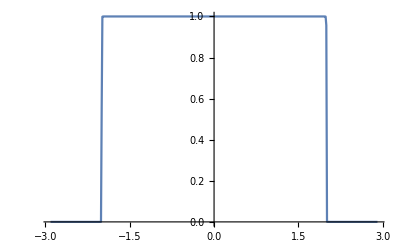

```mathematica
row=1;col=5;ϵ=0.;tV=1.;tH=1.;η=0.001;τSc=1.;
alpha = DiagonalMatrix[Table[ϵ,row]]+If[row>1,DiagonalMatrix[Table[tV,row-1],1]+DiagonalMatrix[Table[tV,row-1],-1],0];
alpha//MatrixForm;
beta =  DiagonalMatrix[Table[tH,row]];
beta//MatrixForm;

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alpha,{col}],Band[{1,row+1}]->Table[beta,{col-1}],Band[{row+1,1}]->Table[beta,{col-1}]},{row*col,row*col} ];
Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm]


transmission =Table[
HS =alpha; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[E1 IdentityMatrix[Length@HS]-HS+ⅈ η]; (*Surface Green's function*)
τS= DiagonalMatrix[Table[τSc,row]]; (*Coupling between source and lead*)
GS11=Array[x,{Length@HS ,Length@HS}]; (*Solve dyson equation*)
f=(gS11.(τS^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@HS *Length@HS}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian},{j,1,Length@Hamiltonian}]];
ΣD= ArrayFlatten[Table[If[i==j==Length@Hamiltonian,ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian},{j,1,Length@Hamiltonian}]];
ΓS =-2Im[ΣS];
ΓD=-2Im[ΣD];
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-2.91,2.91,0.0123}];

ListLinePlot[transmission ,PlotRange->All]
```

### Hamiltonian (only 1D chain )(Old method)

Hamiltonian of the system : (0 | 1. | 0 | 0 | 0
1. | 0 | 1. | 0 | 0
0 | 1. | 0 | 1. | 0
0 | 0 | 1. | 0 | 1.
0 | 0 | 0 | 1. | 0)

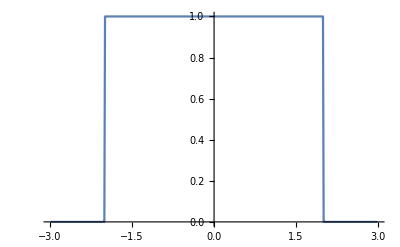

```mathematica
row=1;col=5;ϵ=0.;tV=1.;tH=1.;η=0.0001;τSc=1.;
alpha = DiagonalMatrix[Table[ϵ,row]]+If[row>1,DiagonalMatrix[Table[tV,row-1],1]+DiagonalMatrix[Table[tV,row-1],-1],0];
alpha//MatrixForm;
beta =  DiagonalMatrix[Table[tH,row]];
beta//MatrixForm;

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alpha,{col}],Band[{1,row+1}]->Table[beta,{col-1}],Band[{row+1,1}]->Table[beta,{col-1}]},{row*col,row*col} ];
Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm]


leftE=-2.99;rightE=2.99;stepE=0.0123;t0=1;τS=1;
transmission=Table[
ΣS=ArrayFlatten@Table[If[i==j==1,τS^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{i,1,Length@Hamiltonian},{j,1,Length@Hamiltonian}];
ΣD=ArrayFlatten@Table[If[i==j==Length@Hamiltonian,τS^2/(2 t0^2)((E1-ϵ)-ⅈ √(4 t0^2-(E1-ϵ)^2)),0],{i,1,Length@Hamiltonian},{j,1,Length@Hamiltonian}];
ΓS=-2Im[ΣS];
ΓD=-2Im[ΣD];
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,leftE,rightE,stepE}];

ListLinePlot[transmission]
```

### Hamiltonian (only 1D Ladder )(for single point energy)

```mathematica
row=4;col=5;ϵ=0.;tV=1.;tH=1.;η=0.001;τSc=1.;
alpha = DiagonalMatrix[Table[ϵ,row]]+If[row>1,DiagonalMatrix[Table[tV,row-1],1]+DiagonalMatrix[Table[tV,row-1],-1],0];
alpha//MatrixForm;
beta =  DiagonalMatrix[Table[tH,row]];
beta//MatrixForm;

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alpha,{col}],Band[{1,row+1}]->Table[beta,{col-1}],Band[{row+1,1}]->Table[beta,{col-1}]},{row*col,row*col} ];
Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm]

E1=0;
HS =alpha; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1-+ⅈ η) IdentityMatrix[Length@HS]-HS]; (*Surface Green's function*)
τS= DiagonalMatrix[Table[τSc,row]]; (*Coupling between source and lead*)
GS11=Array[x,{Length@HS ,Length@HS}]; (*Solve dyson equation*)

f=(gS11.(τS^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@HS *Length@HS}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian-(row-1)},{j,1,Length@Hamiltonian-(row-1)}]];
ΣD= ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(row-1),ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian-(row-1)},{j,1,Length@Hamiltonian-(row-1)}]];
ΓS =-2Im[ΣS];
ΓD=-2Im[ΣD];

Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]
Print["Done  ",Length@ΣS," ",Length@ΣD]
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
 Chop[ Tr[ΓS.GR.ΓD.GA]]
```

Hamiltonian of the system : (0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 1. | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 1. | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 1. | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 1. | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 1. | 0)

(0.+0.850151 ⅈ | -0.49962+0. ⅈ | 0.-0.16246 ⅈ | 0.0000726541+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.49962+0. ⅈ | 0.+0.687691 ⅈ | -0.499547+0. ⅈ | 0.-0.16246 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.16246 ⅈ | -0.499547+0. ⅈ | 0.+0.687691 ⅈ | -0.49962+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0000726541+0. ⅈ | 0.-0.16246 ⅈ | -0.49962+0. ⅈ | 0.+0.850151 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.850151 ⅈ | -0.49962+0. ⅈ | 0.-0.16246 ⅈ | 0.0000726541+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.49962+0. ⅈ | 0.+0.687691 ⅈ | -0.499547+0. ⅈ | 0.-0.16246 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.16246 ⅈ | -0.499547+0. ⅈ | 0.+0.687691 ⅈ | -0.49962+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000726541+0. ⅈ | 0.-0.16246 ⅈ | -0.49962+0. ⅈ | 0.+0.850151 ⅈ)(-1.7003 | 0. | 0.324919 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | -1.37538 | 0. | 0.324919 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.324919 | 0. | -1.37538 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0.324919 | 0. | -1.7003 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.7003 | 0. | 0.324919 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | -1.37538 | 0. | 0.324919
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.324919 | 0. | -1.37538 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0.324919 | 0. | -1.7003)

Done  20 20

4.

### Hamiltonian (only 1D Ladder )(with energy variation)

(0.)

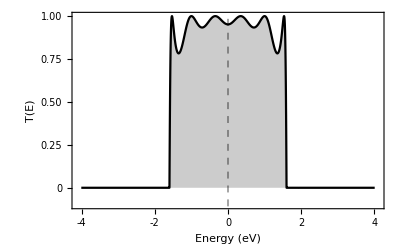

```mathematica
row=1;col=10;ϵ=0.;tV=1.;tH=1.;η=0.00001;τSc=.8;
alpha = DiagonalMatrix[Table[ϵ,row]]+If[row>1,DiagonalMatrix[Table[tV,row-1],1]+DiagonalMatrix[Table[tV,row-1],-1],0];
alpha//MatrixForm;
beta =  DiagonalMatrix[Table[tH,row]];
beta//MatrixForm;

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alpha,{col}],Band[{1,row+1}]->Table[beta,{col-1}],Band[{row+1,1}]->Table[beta,{col-1}]},{row*col,row*col} ];
(*Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm];*)

E1=0;
transmission =Table[
HS =alpha; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@HS]-HS]; (*Surface Green's function*)
τS= DiagonalMatrix[Table[τSc,row]]; (*Coupling between source and lead*)
GS11=Array[x,{Length@HS ,Length@HS}]; (*Solve dyson equation*)
f=(gS11.(τS^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@HS *Length@HS}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian-(row-1)},{j,1,Length@Hamiltonian-(row-1)}]];
ΣD= ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(row-1),ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian-(row-1)},{j,1,Length@Hamiltonian-(row-1)}]];
ΓS =-2Im[ΣS];
ΓD=-2Im[ΣD];

(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.0013}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->{{-4.1,4.1},{-.1,1}},PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
```

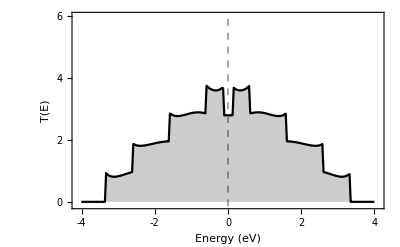

```mathematica
row=5;col=6;ϵ=0.;tV=1.;tH=1.;η=0.001;τSc=.8;
alpha = DiagonalMatrix[Table[ϵ,row]]+If[row>1,DiagonalMatrix[Table[tV,row-1],1]+DiagonalMatrix[Table[tV,row-1],-1],0];
alpha//MatrixForm;
beta =  DiagonalMatrix[Table[tH,row]];
beta//MatrixForm;

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alpha,{col}],Band[{1,row+1}]->Table[beta,{col-1}],Band[{row+1,1}]->Table[beta,{col-1}]},{row*col,row*col} ];
(*Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm];*)

HS =alpha; (*Surface Hamiltonian of the Source-Lead*)
τS= DiagonalMatrix[Table[τSc,row]]; (*Coupling between source and lead*)
GS11=Array[x,{Length@HS ,Length@HS}]; (*Solve dyson equation*)

transmission =Table[
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@HS]-HS]; (*Surface Green's function*)
f=(gS11.(τS^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@HS *Length@HS}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian-(row-1)},{j,1,Length@Hamiltonian-(row-1)}]];
ΣD= ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(row-1),ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian-(row-1)},{j,1,Length@Hamiltonian-(row-1)}]];
ΓS =-2Im[ΣS];
ΓD=-2Im[ΣD];

(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.0323}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->{{-4.1,4.1},{-.1,6}},PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
```

### Hamiltonian (only 1D Ladder )(with energy variation)(change lead hopping and coupling)

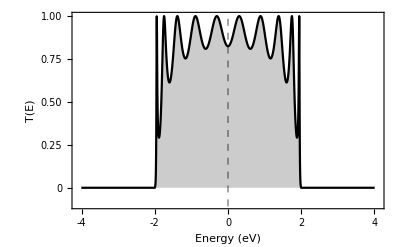

```mathematica
row=1;col=10;ϵ=0.;tV=1.;tH=1.;η=0.00001;τSc=.8;τlead=1;
alpha = DiagonalMatrix[Table[ϵ,row]]+If[row>1,DiagonalMatrix[Table[tV,row-1],1]+DiagonalMatrix[Table[tV,row-1],-1],0];
alpha//MatrixForm;
beta =  DiagonalMatrix[Table[tH,row]];
beta//MatrixForm;

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alpha,{col}],Band[{1,row+1}]->Table[beta,{col-1}],Band[{row+1,1}]->Table[beta,{col-1}]},{row*col,row*col} ];
(*Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm];*)

E1=0;
transmission =Table[
HS =alpha; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@HS]-HS]; (*Surface Green's function*)
τ0= DiagonalMatrix[Table[τlead,row]]; 
τS= DiagonalMatrix[Table[τSc,row]];(*Coupling between source and lead*)
GS11=Array[x,{Length@HS ,Length@HS}]; (*Solve dyson equation*)
f=(gS11.(τ0^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@HS *Length@HS}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian-(row-1)},{j,1,Length@Hamiltonian-(row-1)}]];
ΣD= ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(row-1),ConjugateTranspose[τS].Partition[Values[sol],{Length@τS}].τS,0],{i,1,Length@Hamiltonian-(row-1)},{j,1,Length@Hamiltonian-(row-1)}]];
ΓS =-2Im[ΣS];
ΓD=-2Im[ΣD];

(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.0013}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->{{-4.1,4.1},{-.1,1}},PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
```

## Transport in 1D chain & square lattice- Solving Dyson equation-(Final)

### 1D - Chain to Square lattice

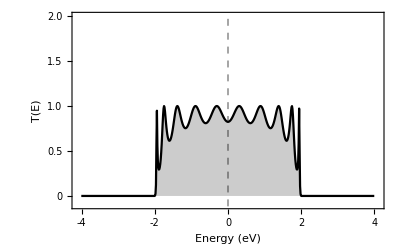

```mathematica
(******************************************* System Parameters ************************************************)
channelLength = 10; channelWidth = 1;
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = .8; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;

(******************************************* System Hamiltonian ************************************************)
alphaSystem = DiagonalMatrix[Table[onsiteChannel,channelWidth]]+If[channelWidth>1,DiagonalMatrix[Table[ tVerticalChannel,channelWidth-1],1]+DiagonalMatrix[Table[ tVerticalChannel,channelWidth-1],-1],0];
alphaSystem//MatrixForm;
betaSystem =  DiagonalMatrix[Table[ tHorizontalChannel,channelWidth]];
betaSystem//MatrixForm;

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alphaSystem,{channelLength }],Band[{1,channelWidth+1}]->Table[betaSystem,{channelLength -1}],Band[{channelWidth+1,1}]->Table[betaSystem,{channelLength -1}]},{channelWidth*channelLength ,channelWidth*channelLength } ];
(*Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm];*)

(******************************************* System Lead Couplings ************************************************)
τSource= DiagonalMatrix[Table[τSC,channelWidth]];
τDrain= DiagonalMatrix[Table[τCD,channelWidth]];

E1=0;
transmission =Table[
(******************************************* Self energy for Source ************************************************)
alphaSource =alphaSystem; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
τ0Source= DiagonalMatrix[Table[tHorizontalSource,channelWidth]]; 
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.(τ0Source^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(channelWidth-1)},{j,1,Length@Hamiltonian-(channelWidth-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
alphaDrain=alphaSource; (*Surface Hamiltonian of the Drain-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
τ0Drain= DiagonalMatrix[Table[tHorizontalDrain,channelWidth]]; 
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.(τ0Drain^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(channelWidth-1),ConjugateTranspose[τDrain].Partition[Values[sol],{Length@τDrain}].τDrain,0],{i,1,Length@Hamiltonian-(channelWidth-1)},{j,1,Length@Hamiltonian-(channelWidth-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.013}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->{{-4.1,4.1},{-.1,2}},PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
```

## To solve quadratic matrix equation

```mathematica
n=2;
X=Array[x,{n,n}];
a=RandomReal[{-1,1},{n,n}];
b=RandomReal[{-1,1},{n,n}];
c=RandomReal[{-1,1},{n,n}];
f=(a.X+b).X+c;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[X][[i]],0},{i,1,n n}]]
Partition[Values[sol],{1}]
f/. sol
```

{x[1,1]→0.795916,x[1,2]→1.01526,x[2,1]→-2.1416,x[2,2]→-1.61306}

{{0.795916},{1.01526},{-2.1416},{-1.61306}}

{{-3.33067×10^-16,-1.11022×10^-16},{4.44089×10^-16,2.22045×10^-16}}

```mathematica
(*Define a square matrix*)modifiedMatrix=.;
matrix=RandomInteger[10,{6,6}];
modifiedMatrix[mat_,num_]:=Module[{rowsAdded,rowsDeleted,colsAdded,colsDeleted},(*Add two rows of zeros at the top*)
rowsAdded=Join[ConstantArray[0,{num,Length[mat[[1]]]}],mat];
rowsDeleted=Take[rowsAdded,Length[rowsAdded]-num];
colsAdded=Join[ConstantArray[0,{Length[rowsDeleted],num}],rowsDeleted,2];
colsDeleted=Take[colsAdded,All,Length[colsAdded[[1]]]-num];
colsDeleted];

(*Display results*)
matrix//MatrixForm
modifiedMatrix[matrix,1]//MatrixForm
```

(3 | 10 | 1 | 8 | 3 | 9
8 | 8 | 3 | 5 | 1 | 2
8 | 8 | 9 | 0 | 0 | 7
8 | 5 | 5 | 5 | 0 | 0
3 | 6 | 3 | 3 | 1 | 9
7 | 5 | 1 | 10 | 7 | 6)

(0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 10 | 1 | 8 | 3
0 | 8 | 8 | 3 | 5 | 1
0 | 8 | 8 | 9 | 0 | 0
0 | 8 | 5 | 5 | 5 | 0
0 | 3 | 6 | 3 | 3 | 1)

```mathematica
AllRealQ[matrix_]:=AllTrue[Flatten[matrix],Im[#]==0&]
AllRealQ[ΣS]
```

False

## Graphene

### Zigzag

#### Model

```mathematica
atomPositions = {{(√3)/2,-1},{0,-1/2},{0,1/2},{(√3)/2,1}};
ax = {√3,0};
ay = {0,3};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=3; ny=2;
supercellCoordinates=GenerateSupercell[atomPositions,ax,ay,nx,ny];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]
```

-Graphics3D-

#### Hamiltonian and transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

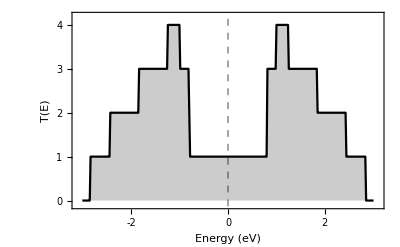

```mathematica
(******************************************* System Parameters ************************************************)
channelLength = 2; channelWidth = 2; unitAtoms=4;
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;

(******************************************* System Hamiltonian ************************************************)
unitAlpha = DiagonalMatrix[Table[onsiteChannel,unitAtoms]]+If[unitAtoms>1,DiagonalMatrix[Table[ tVerticalChannel,unitAtoms-1],1]+DiagonalMatrix[Table[ tVerticalChannel,unitAtoms-1],-1],0];
unitBetax=Table[If[i==2 && j==1,tHorizontalChannel,If[j==unitAtoms && i== unitAtoms-1,tHorizontalChannel,0]],{j,1,unitAtoms},{i,1,unitAtoms}];
unitBetay=Table[If[i==1 && j==unitAtoms,tVerticalChannel,0],{j,1,unitAtoms},{i,1,unitAtoms}];
Map[MatrixForm,{unitAlpha,unitBetax,unitBetay}];

alphaSystem = SparseArray[{Band[{1,1}]->Table[unitAlpha,{channelWidth }],Band[{1,unitAtoms+1}]->Table[unitBetay,{channelWidth -1}],Band[{unitAtoms+1,1}]->Table[Transpose@unitBetay,{channelWidth -1}]},{channelWidth*unitAtoms,channelWidth*unitAtoms } ];
betaSystem =SparseArray[Band[{1,1}]->Table[unitBetax,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
Map[MatrixForm,{alphaSystem,betaSystem}];

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alphaSystem,{channelLength }],Band[{1,Length@alphaSystem+1}]->Table[betaSystem,{channelLength -1}],Band[{Length@alphaSystem+1,1}]->Table[Transpose@betaSystem,{channelLength -1}]},{channelLength *Length@alphaSystem,channelLength*Length@alphaSystem } ];
(*Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm];*)

(******************************************* System Lead Couplings ************************************************)
unitBetaSCx=Table[If[i==2 && j==1,τSC,If[j==unitAtoms && i== unitAtoms-1,tHorizontalChannel,0]],{j,1,unitAtoms},{i,1,unitAtoms}];
unitBetaCDx=unitBetaSCx;
τSource=SparseArray[Band[{1,1}]->Table[unitBetaSCx,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
τDrain= SparseArray[Band[{1,1}]->Table[unitBetaCDx,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;

τSource == betaSystem ==τ0Source ;

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
alphaSource =alphaSystem; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
unitBetaS0x=Table[If[i==2 && j==1,τSC,If[j==unitAtoms && i== unitAtoms-1,tHorizontalSource,0]],{j,1,unitAtoms},{i,1,unitAtoms}];
τ0Source= SparseArray[Band[{1,1}]->Table[unitBetaS0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
alphaDrain=alphaSource; (*Surface Hamiltonian of the Drain-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
unitBetaD0x=unitBetaS0x;
τ0Drain= SparseArray[Band[{1,1}]->Table[unitBetaD0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(channelWidth*unitAtoms-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-3.01,3.01,0.017}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->{{-3.1,3.1},{-.1,4.2}},PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
```

### Armchair

#### Model

```mathematica
atomPositions = {{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}};
ax = {3,0};
ay = {0,√3};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=3; ny=3;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->700]
```

-Graphics3D-

## 2 and 4 Atoms Square Lattice

### 2 Atoms square lattice (vertical)

#### Model

```mathematica
atomPositions = {{0,0},{0,1}};
ax = {1,0};
ay = {0,2};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=4; ny=2;
supercellCoordinates=GenerateSupercell[atomPositions,ax,ay,nx,ny];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]
```

-Graphics3D-

#### Transmission

Hamiltonian of the system : (0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0)

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

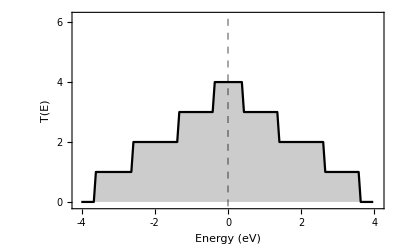

```mathematica
(******************************************* System Parameters ************************************************)
channelLength = 2; channelWidth = 2; unitAtoms=2;
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;

(******************************************* System Hamiltonian ************************************************)
unitAlpha = DiagonalMatrix[Table[onsiteChannel,unitAtoms]]+If[unitAtoms>1,DiagonalMatrix[Table[ tVerticalChannel,unitAtoms-1],1]+DiagonalMatrix[Table[ tVerticalChannel,unitAtoms-1],-1],0];
unitBetax=DiagonalMatrix[Table[tHorizontalChannel,unitAtoms]];
unitBetay=Table[If[i==1 && j==unitAtoms,tVerticalChannel,0],{j,1,unitAtoms},{i,1,unitAtoms}];
(*Map[MatrixForm,{unitAlpha,unitBetax,unitBetay}]*)

alphaSystem = SparseArray[{Band[{1,1}]->Table[unitAlpha,{channelWidth }],Band[{1,unitAtoms+1}]->Table[unitBetay,{channelWidth -1}],Band[{unitAtoms+1,1}]->Table[Transpose@unitBetay,{channelWidth -1}]},{channelWidth*unitAtoms,channelWidth*unitAtoms } ];
betaSystem =SparseArray[Band[{1,1}]->Table[unitBetax,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
(*Map[MatrixForm,{alphaSystem,betaSystem}]*)

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alphaSystem,{channelLength }],Band[{1,Length@alphaSystem+1}]->Table[betaSystem,{channelLength -1}],Band[{Length@alphaSystem+1,1}]->Table[Transpose@betaSystem,{channelLength -1}]},{channelLength *Length@alphaSystem,channelLength*Length@alphaSystem } ];
Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm];

(******************************************* System Lead Couplings ************************************************)
unitBetaSCx=DiagonalMatrix[Table[tHorizontalSource,unitAtoms]];
unitBetaCDx=unitBetaSCx;
τSource=SparseArray[Band[{1,1}]->Table[unitBetaSCx,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
τDrain=SparseArray[Band[{1,1}]->Table[unitBetaCDx,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
τSource//MatrixForm

E1=0.;
transmission =Table[
(******************************************* Self energy for Source ************************************************)
alphaSource =alphaSystem; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
unitBetaS0x=DiagonalMatrix[Table[tHorizontalSource,unitAtoms]];
τ0Source= SparseArray[Band[{1,1}]->Table[unitBetaS0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.τ0Source.GS11.ConjugateTranspose[τ0Source]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
alphaDrain=alphaSource; (*Surface Hamiltonian of the Drain-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
unitBetaD0x=unitBetaS0x;
τ0Drain= SparseArray[Band[{1,1}]->Table[unitBetaD0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(channelWidth*unitAtoms-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.057}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->{{-4.1,4.1},{-.1,6.2}},PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
```

```mathematica
E1=0.;
(******************************************* Self energy for Source ************************************************)
alphaSource =alphaSystem; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
unitBetaS0x=DiagonalMatrix[Table[tHorizontalSource,unitAtoms]];
τ0Source= SparseArray[Band[{1,1}]->Table[unitBetaS0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.(τ0Source^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
alphaDrain=alphaSource; (*Surface Hamiltonian of the Drain-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
unitBetaD0x=unitBetaS0x;
τ0Drain= SparseArray[Band[{1,1}]->Table[unitBetaD0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.(τ0Drain^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(channelWidth*unitAtoms-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]
```

(0.-0.850646 ⅈ | -0.499996+0. ⅈ | 0.+0.16246 ⅈ | 7.26543×10^-7+0. ⅈ | 0 | 0 | 0 | 0
-0.499996+0. ⅈ | 0.-0.688186 ⅈ | -0.499995+0. ⅈ | 0.+0.16246 ⅈ | 0 | 0 | 0 | 0
0.+0.16246 ⅈ | -0.499995+0. ⅈ | 0.-0.688186 ⅈ | -0.499996+0. ⅈ | 0 | 0 | 0 | 0
7.26543×10^-7+0. ⅈ | 0.+0.16246 ⅈ | -0.499996+0. ⅈ | 0.-0.850646 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.850646 ⅈ | -0.499996+0. ⅈ | 0.+0.16246 ⅈ | 7.26543×10^-7+0. ⅈ
0 | 0 | 0 | 0 | -0.499996+0. ⅈ | 0.-0.688186 ⅈ | -0.499995+0. ⅈ | 0.+0.16246 ⅈ
0 | 0 | 0 | 0 | 0.+0.16246 ⅈ | -0.499995+0. ⅈ | 0.-0.688186 ⅈ | -0.499996+0. ⅈ
0 | 0 | 0 | 0 | 7.26543×10^-7+0. ⅈ | 0.+0.16246 ⅈ | -0.499996+0. ⅈ | 0.-0.850646 ⅈ)(1.70129 | 0. | -0.32492 | 0. | 0 | 0 | 0 | 0
0. | 1.37637 | 0. | -0.32492 | 0 | 0 | 0 | 0
-0.32492 | 0. | 1.37637 | 0. | 0 | 0 | 0 | 0
0. | -0.32492 | 0. | 1.70129 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.70129 | 0. | -0.32492 | 0.
0 | 0 | 0 | 0 | 0. | 1.37637 | 0. | -0.32492
0 | 0 | 0 | 0 | -0.32492 | 0. | 1.37637 | 0.
0 | 0 | 0 | 0 | 0. | -0.32492 | 0. | 1.70129)

### 2 Atoms square lattice (horizontal)

#### Model

```mathematica
atomPositions = {{0,0},{1,0}};
ax = {2,0};
ay = {0,1};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=2; ny=2;
supercellCoordinates=GenerateSupercell[atomPositions,ax,ay,nx,ny];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];


(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]
```

-Graphics3D-

#### Transmission

Hamiltonian of the system : (0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)

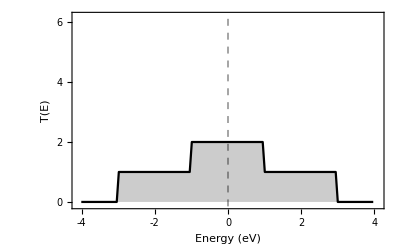

```mathematica
(******************************************* System Parameters ************************************************)
channelLength = 2; channelWidth = 2; unitAtoms=2;
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;

(******************************************* System Hamiltonian ************************************************)
unitAlpha = DiagonalMatrix[Table[onsiteChannel,unitAtoms]]+If[unitAtoms>1,DiagonalMatrix[Table[ tVerticalChannel,unitAtoms-1],1]+DiagonalMatrix[Table[ tVerticalChannel,unitAtoms-1],-1],0];
unitBetax=Table[If[i==1 && j==unitAtoms,tVerticalChannel,0],{j,1,unitAtoms},{i,1,unitAtoms}];
unitBetay=DiagonalMatrix[Table[tHorizontalChannel,unitAtoms]];
Map[MatrixForm,{unitAlpha,unitBetax,unitBetay}];

alphaSystem = SparseArray[{Band[{1,1}]->Table[unitAlpha,{channelWidth }],Band[{1,unitAtoms+1}]->Table[unitBetay,{channelWidth -1}],Band[{unitAtoms+1,1}]->Table[Transpose@unitBetay,{channelWidth -1}]},{channelWidth*unitAtoms,channelWidth*unitAtoms } ];
betaSystem =SparseArray[Band[{1,1}]->Table[unitBetax,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
Map[MatrixForm,{alphaSystem,betaSystem}];

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alphaSystem,{channelLength }],Band[{1,Length@alphaSystem+1}]->Table[betaSystem,{channelLength -1}],Band[{Length@alphaSystem+1,1}]->Table[Transpose@betaSystem,{channelLength -1}]},{channelLength *Length@alphaSystem,channelLength*Length@alphaSystem } ];
Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm];

(******************************************* System Lead Couplings ************************************************)
unitBetaSCx=Table[If[i==1 && j==unitAtoms,tVerticalChannel,0],{j,1,unitAtoms},{i,1,unitAtoms}];
unitBetaCDx=unitBetaSCx;
τSource=SparseArray[Band[{1,1}]->Table[unitBetaSCx,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
τDrain=SparseArray[Band[{1,1}]->Table[unitBetaCDx,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
τSource//MatrixForm;

E1=0.;
transmission =Table[
(******************************************* Self energy for Source ************************************************)
alphaSource =alphaSystem; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
unitBetaS0x=Table[If[i==1 && j==unitAtoms,tVerticalChannel,0],{j,1,unitAtoms},{i,1,unitAtoms}];
τ0Source= SparseArray[Band[{1,1}]->Table[unitBetaS0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
alphaDrain=alphaSource; (*Surface Hamiltonian of the Drain-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
unitBetaD0x=unitBetaS0x;
τ0Drain= SparseArray[Band[{1,1}]->Table[unitBetaD0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(channelWidth*unitAtoms-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.057}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->{{-4.1,4.1},{-.1,6.2}},PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
```

```mathematica
E1=0.5;
(******************************************* Self energy for Source ************************************************)
alphaSource =alphaSystem; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
unitBetaS0x=DiagonalMatrix[Table[tHorizontalSource,unitAtoms]];
τ0Source= SparseArray[Band[{1,1}]->Table[unitBetaS0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
alphaDrain=alphaSource; (*Surface Hamiltonian of the Drain-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
unitBetaD0x=unitBetaS0x;
τ0Drain= SparseArray[Band[{1,1}]->Table[unitBetaD0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(channelWidth*unitAtoms-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
 Chop[ Tr[ΓS.GR.ΓD.GA]]
```

(0.0625008-0.649479 ⅈ | 0.+0. ⅈ | -0.312499-0.165357 ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0
-0.312499-0.165357 ⅈ | 0.+0. ⅈ | 0.0625008-0.649479 ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.0625008-0.649479 ⅈ | 0.+0. ⅈ | -0.312499-0.165357 ⅈ
0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0.+0. ⅈ | -0.312499-0.165357 ⅈ | 0.+0. ⅈ | 0.0625008-0.649479 ⅈ)(1.29896 | 0. | 0.330715 | 0. | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0 | 0 | 0 | 0
0.330715 | 0. | 1.29896 | 0. | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0. | 1.29896 | 0. | 0.330715
0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0. | 0.330715 | 0. | 1.29896)

1.77387

### 4 Atoms square lattice

#### Model

```mathematica
atomPositions = {{0,0},{0,1},{1,0},{1,1}};
ax = {2,0};
ay = {0,2};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=3; ny=3;
supercellCoordinates=GenerateSupercell[atomPositions,ax,ay,nx,ny];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]
```

-Graphics3D-

#### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

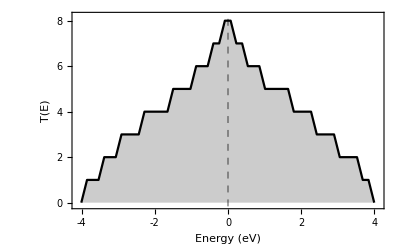

```mathematica
(******************************************* System Parameters ************************************************)
channelLength = 4; channelWidth = 4; unitAtoms=4;
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;

(******************************************* System Hamiltonian ************************************************)
unitAlpha = {{onsiteChannel, tHorizontalChannel, tHorizontalChannel,0},{ tHorizontalChannel,onsiteChannel,0, tHorizontalChannel},{ tHorizontalChannel,0,onsiteChannel, tHorizontalChannel},{0, tHorizontalChannel, tHorizontalChannel,onsiteChannel}};
unitBetax={{0,0,0,0},{0,0,0,0},{ tHorizontalChannel,0,0,0},{0, tHorizontalChannel,0,0}};
unitBetay={{0,0,0,0},{tVerticalChannel ,0,0,0},{0,0,0,0},{0,0,tVerticalChannel ,0}};
Map[MatrixForm,{unitAlpha,unitBetax,unitBetay}];

alphaSystem = SparseArray[{Band[{1,1}]->Table[unitAlpha,{channelWidth }],Band[{1,unitAtoms+1}]->Table[unitBetay,{channelWidth -1}],Band[{unitAtoms+1,1}]->Table[Transpose@unitBetay,{channelWidth -1}]},{channelWidth*unitAtoms,channelWidth*unitAtoms } ];
betaSystem =SparseArray[Band[{1,1}]->Table[unitBetax,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
Map[MatrixForm,{alphaSystem,betaSystem}];

Hamiltonian = SparseArray[{Band[{1,1}]->Table[alphaSystem,{channelLength }],Band[{1,Length@alphaSystem+1}]->Table[betaSystem,{channelLength -1}],Band[{Length@alphaSystem+1,1}]->Table[Transpose@betaSystem,{channelLength -1}]},{channelLength *Length@alphaSystem,channelLength*Length@alphaSystem } ];
(*Print["Hamiltonian of the system : ", Hamiltonian//MatrixForm];*)

(******************************************* System Lead Couplings ************************************************)
unitBetaSCx={{0,0,0,0},{0,0,0,0},{ τSC,0,0,0},{0, τSC,0,0}};
unitBetaCDx=unitBetaSCx;
τSource=SparseArray[Band[{1,1}]->Table[unitBetaSCx,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
τDrain= SparseArray[Band[{1,1}]->Table[unitBetaCDx,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
Map[MatrixForm,{τSource,τDrain}];

E1=0.;
transmission =Table[
(******************************************* Self energy for Source ************************************************)
alphaSource =alphaSystem; (*Surface Hamiltonian of the Source-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
unitBetaS0x={{0,0,0,0},{0,0,0,0},{ tHorizontalSource,0,0,0},{0, tHorizontalSource,0,0}};
τ0Source= SparseArray[Band[{1,1}]->Table[unitBetaS0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
alphaDrain=alphaSource; (*Surface Hamiltonian of the Drain-Lead*)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
unitBetaD0x=unitBetaS0x;
τ0Drain= SparseArray[Band[{1,1}]->Table[unitBetaD0x,{channelWidth }],{channelWidth*unitAtoms,channelWidth*unitAtoms }] ;
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(channelWidth*unitAtoms-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)},{j,1,Length@Hamiltonian-(channelWidth*unitAtoms-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->{{-4.1,4.1},{-.1,8.2}},PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
```

## 1 D chain to 2 D square lattice - hopping generated from geometry (Spin-less : Success)

### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{0,0}(*,{0,1},{1,0},{1,1}*)};
ax = {1,0};
ay = {0,1};
nx=10; ny=1;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2}},{2,{1,3}},{3,{2,4}},{4,{3,5}},{5,{4,6}},{6,{5,7}},{7,{6,8}},{8,{7,9}},{9,{8,10}},{10,{9}}}

### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

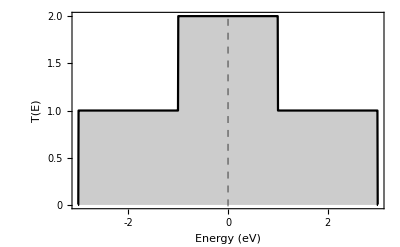

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1.; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,2}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-3.01,3.01,0.0057}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

### Transmission (inspection)

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,2}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
(*transmission =ParallelTable[*)
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];*)
```

(0.-0.86602 ⅈ | -0.499997+0. ⅈ | 0 | 0 | 0 | 0
-0.499997+0. ⅈ | 0.-0.86602 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.86602 ⅈ | -0.499997+0. ⅈ
0 | 0 | 0 | 0 | -0.499997+0. ⅈ | 0.-0.86602 ⅈ)(1.73204 | 0. | 0 | 0 | 0 | 0
0. | 1.73204 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.73204 | 0.
0 | 0 | 0 | 0 | 0. | 1.73204)

## Graphene (hopping generated from geometry) (Spin-less : Success)

### Zigzag

#### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{(√3)/2,-1},{0,-1/2},{0,1/2},{(√3)/2,1}};
ax = {√3,0};
ay = {0,3};
nx=4; ny=2;
supercellCoordinates=GenerateSupercell[atomPositions,ax,ay,nx,ny];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,10}},{2,{1,3}},{3,{2,4}},{4,{3,5,11}},{5,{4,6,14}},{6,{5,7}},{7,{6,8}},{8,{7,15}},{9,{10,18}},{10,{1,9,11}},{11,{4,10,12}},{12,{11,13,19}},{13,{12,14,22}},{14,{5,13,15}},{15,{8,14,16}},{16,{15,23}},{17,{18,26}},{18,{9,17,19}},{19,{12,18,20}},{20,{19,21,27}},{21,{20,22,30}},{22,{13,21,23}},{23,{16,22,24}},{24,{23,31}},{25,{26}},{26,{17,25,27}},{27,{20,26,28}},{28,{27,29}},{29,{28,30}},{30,{21,29,31}},{31,{24,30,32}},{32,{31}}}

#### Transmission

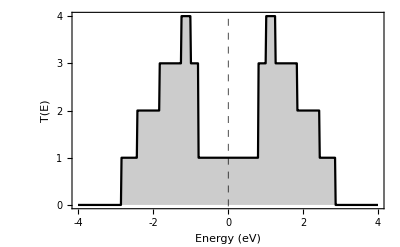

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

### Armchair

#### Model

```mathematica
atomPositions = {{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}};
ax = {3,0};
ay = {0,√3};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=4; ny=3;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->700]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{4,5}},{2,{5,6}},{3,{6}},{4,{1,7}},{5,{1,2,8}},{6,{2,3,9}},{7,{4,10}},{8,{5,10,11}},{9,{6,11,12}},{10,{7,8,13}},{11,{8,9,14}},{12,{9,15}},{13,{10,16,17}},{14,{11,17,18}},{15,{12,18}},{16,{13,19}},{17,{13,14,20}},{18,{14,15,21}},{19,{16,22}},{20,{17,22,23}},{21,{18,23,24}},{22,{19,20,25}},{23,{20,21,26}},{24,{21,27}},{25,{22,28,29}},{26,{23,29,30}},{27,{24,30}},{28,{25,31}},{29,{25,26,32}},{30,{26,27,33}},{31,{28,34}},{32,{29,34,35}},{33,{30,35,36}},{34,{31,32,37}},{35,{32,33,38}},{36,{33,39}},{37,{34,40,41}},{38,{35,41,42}},{39,{36,42}},{40,{37,43}},{41,{37,38,44}},{42,{38,39,45}},{43,{40,46}},{44,{41,46,47}},{45,{42,47,48}},{46,{43,44}},{47,{44,45}},{48,{45}}}

#### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

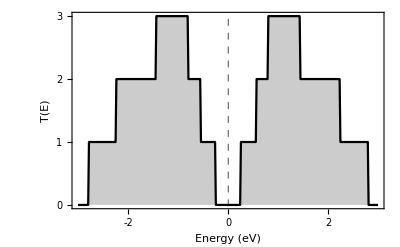

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1.; τCD = τSC; 
onsiteSource=0.; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,12}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@supercellCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-3.01,3.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

## 1 D chain to 2 D square lattice - hopping generated from geometry - (spin-full : Success)

### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{0,0}(*,{0,1},{1,0},{1,1}*)};
ax = {1,0};
ay = {0,1};
nx=10; ny=2;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,3}},{2,{1,4}},{3,{1,4,5}},{4,{2,3,6}},{5,{3,6,7}},{6,{4,5,8}},{7,{5,8,9}},{8,{6,7,10}},{9,{7,10,11}},{10,{8,9,12}},{11,{9,12,13}},{12,{10,11,14}},{13,{11,14,15}},{14,{12,13,16}},{15,{13,16,17}},{16,{14,15,18}},{17,{15,18,19}},{18,{16,17,20}},{19,{17,20}},{20,{18,19}}}

### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

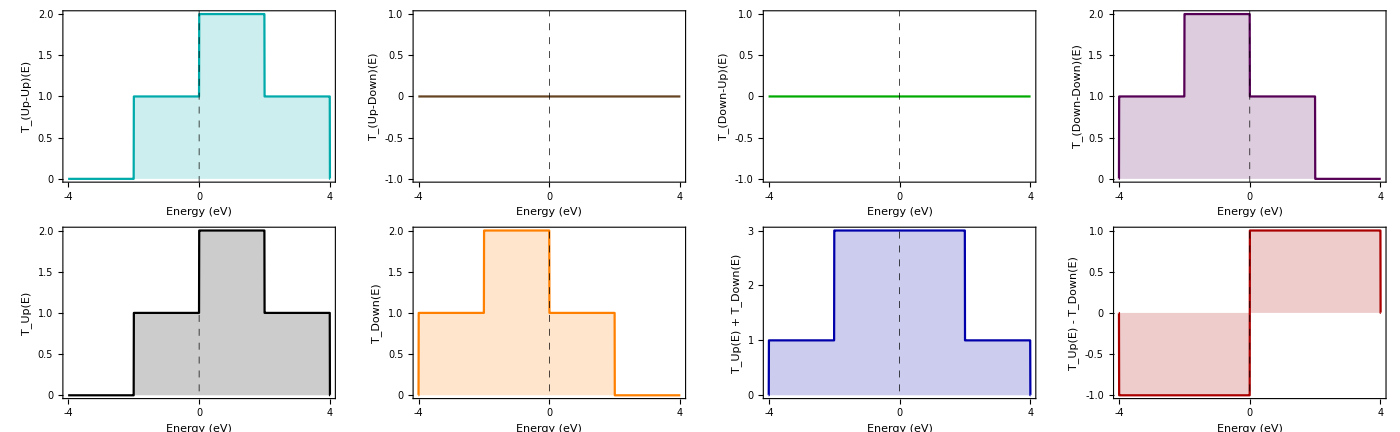

```mathematica
(******************************************* System Parameters ************************************************)
h=1.;r=1;
onsiteChannel={{h,0},{0,-h}}; tHorizontalChannel={{1,0},{0,1}}; tVerticalChannel = {{1,0},{0,1}};
τSC =1.; τCD = τSC; 
tHS=1;tVS=tHS;
onsiteSource={{h,0},{0,-h}}; tHorizontalSource={{tHS,0},{0,tHS}}; tVerticalSource =tHorizontalSource;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,2}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian =ArrayFlatten[ Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource =ArrayFlatten[ Table[If[Hamiltonian[[r,c+2  Max[surfaceElements1]]]==0,0,τSC],{r,2*Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source=ArrayFlatten[Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,tHS],{r,2 *Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΓSUp=Table[If[OddQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
          ΓSDw=Table[If[EvenQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(2 Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
ΓDUp=Table[If[OddQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
	 ΓDDw=Table[If[EvenQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian];
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm];
Map[MatrixForm,{ΓSUp,ΓSDw,ΓDUp,ΓDDw}]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*Print[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]," ", Chop[Tr[ΓSUp.GR.ΓDDw.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDUp.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDDw.GA]]];*)
{E1, Chop[Tr[ΓSUp.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]],Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]+Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]-Chop[Tr[ΓSUp.GR.ΓDDw.GA]]-Chop[Tr[ΓSDw.GR.ΓDDw.GA]]]},{E1,-4.01,4.01,0.0057}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
TUU = ListLinePlot[transmission[[All,{1,2}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Cyan]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUD = ListLinePlot[transmission[[All,{1,3}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Brown]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDU = ListLinePlot[transmission[[All,{1,4}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Green]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDD = ListLinePlot[transmission[[All,{1,5}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Purple]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TU = ListLinePlot[transmission[[All,{1,6}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TD = ListLinePlot[transmission[[All,{1,7}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Orange],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUPlusD = ListLinePlot[transmission[[All,{1,8}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Blue]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) + T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUMinusD = ListLinePlot[transmission[[All,{1,9}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Red]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) - T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
GraphicsGrid[{{TUU,TUD,TDU,TDD},{TU,TD,TUPlusD,TUMinusD}},Spacings->1,ImageSize->1400]
```

```mathematica
MatrixForm@onsiteChannel
```

(1. | 0
0 | -1.)

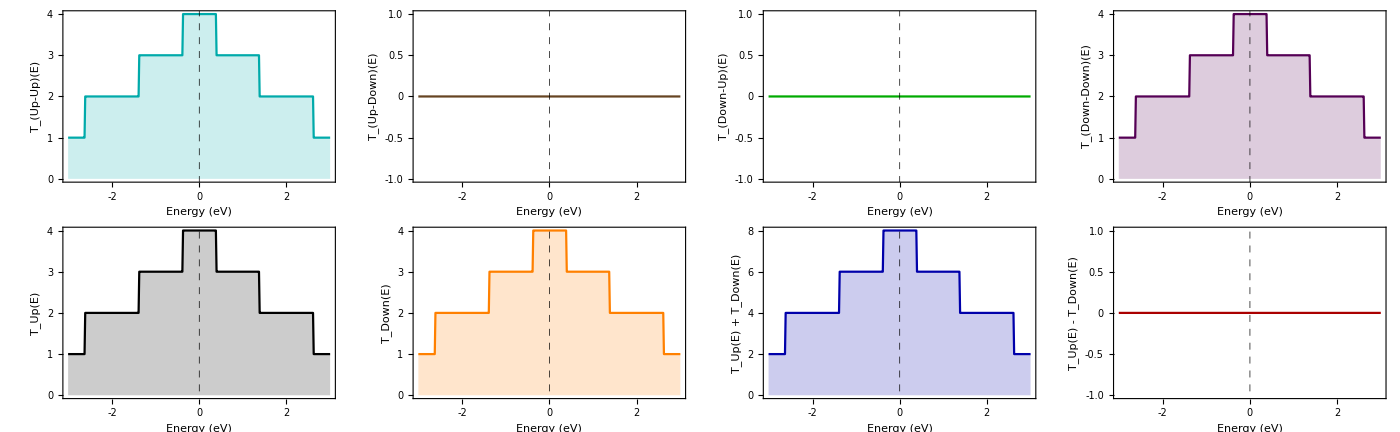

## Graphene (hopping generated from geometry) (Spin-full : Success)

### Zigzag

#### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{(√3)/2,-1},{0,-1/2},{0,1/2},{(√3)/2,1}};
ax = {√3,0};
ay = {0,3};
nx=5; ny=2;
supercellCoordinates=GenerateSupercell[atomPositions,ax,ay,nx,ny];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,10}},{2,{1,3}},{3,{2,4}},{4,{3,5,11}},{5,{4,6,14}},{6,{5,7}},{7,{6,8}},{8,{7,15}},{9,{10,18}},{10,{1,9,11}},{11,{4,10,12}},{12,{11,13,19}},{13,{12,14,22}},{14,{5,13,15}},{15,{8,14,16}},{16,{15,23}},{17,{18,26}},{18,{9,17,19}},{19,{12,18,20}},{20,{19,21,27}},{21,{20,22,30}},{22,{13,21,23}},{23,{16,22,24}},{24,{23,31}},{25,{26,34}},{26,{17,25,27}},{27,{20,26,28}},{28,{27,29,35}},{29,{28,30,38}},{30,{21,29,31}},{31,{24,30,32}},{32,{31,39}},{33,{34}},{34,{25,33,35}},{35,{28,34,36}},{36,{35,37}},{37,{36,38}},{38,{29,37,39}},{39,{32,38,40}},{40,{39}}}

#### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

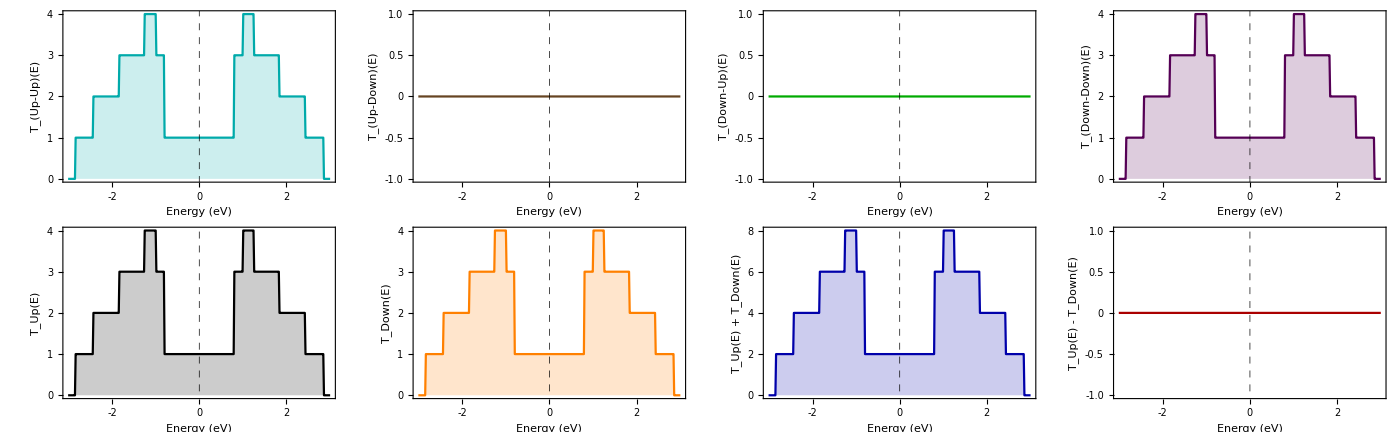

```mathematica
(******************************************* System Parameters ************************************************)
h=0;r=1;
onsiteChannel={{h,0},{0,-h}}; tHorizontalChannel={{1,0},{0,1}}; tVerticalChannel = {{1,0},{0,1}};
τSC =1; τCD = τSC; 
tHS=1;tVS=tHS;
onsiteSource={{h,0},{0,-h}}; tHorizontalSource={{tHS,0},{0,tHS}}; tVerticalSource =tHorizontalSource;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian =ArrayFlatten[ Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource =ArrayFlatten[ Table[If[Hamiltonian[[r,c+2  Max[surfaceElements1]]]==0,0,τSC],{r,2*Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source=ArrayFlatten[Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,tHS],{r,2 *Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΓSUp=Table[If[OddQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
          ΓSDw=Table[If[EvenQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(2 Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
ΓDUp=Table[If[OddQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
	 ΓDDw=Table[If[EvenQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian];
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm];
Map[MatrixForm,{ΓSUp,ΓSDw,ΓDUp,ΓDDw}]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*Print[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]," ", Chop[Tr[ΓSUp.GR.ΓDDw.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDUp.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDDw.GA]]];*)
{E1, Chop[Tr[ΓSUp.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]],Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]+Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]-Chop[Tr[ΓSUp.GR.ΓDDw.GA]]-Chop[Tr[ΓSDw.GR.ΓDDw.GA]]]},{E1,-3.01,3.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
TUU = ListLinePlot[transmission[[All,{1,2}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Cyan]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUD = ListLinePlot[transmission[[All,{1,3}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Brown]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDU = ListLinePlot[transmission[[All,{1,4}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Green]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDD = ListLinePlot[transmission[[All,{1,5}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Purple]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TU = ListLinePlot[transmission[[All,{1,6}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TD = ListLinePlot[transmission[[All,{1,7}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Orange],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUPlusD = ListLinePlot[transmission[[All,{1,8}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Blue]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) + T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUMinusD = ListLinePlot[transmission[[All,{1,9}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Red]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) - T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
GraphicsGrid[{{TUU,TUD,TDU,TDD},{TU,TD,TUPlusD,TUMinusD}},Spacings->1,ImageSize->1400]
```

### Armchair

#### Model

```mathematica
atomPositions = {{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}};
ax = {3,0};
ay = {0,√3};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=4; ny=3;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->700]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{4,5}},{2,{5,6}},{3,{6}},{4,{1,7}},{5,{1,2,8}},{6,{2,3,9}},{7,{4,10}},{8,{5,10,11}},{9,{6,11,12}},{10,{7,8,13}},{11,{8,9,14}},{12,{9,15}},{13,{10,16,17}},{14,{11,17,18}},{15,{12,18}},{16,{13,19}},{17,{13,14,20}},{18,{14,15,21}},{19,{16,22}},{20,{17,22,23}},{21,{18,23,24}},{22,{19,20,25}},{23,{20,21,26}},{24,{21,27}},{25,{22,28,29}},{26,{23,29,30}},{27,{24,30}},{28,{25,31}},{29,{25,26,32}},{30,{26,27,33}},{31,{28,34}},{32,{29,34,35}},{33,{30,35,36}},{34,{31,32,37}},{35,{32,33,38}},{36,{33,39}},{37,{34,40,41}},{38,{35,41,42}},{39,{36,42}},{40,{37,43}},{41,{37,38,44}},{42,{38,39,45}},{43,{40,46}},{44,{41,46,47}},{45,{42,47,48}},{46,{43,44}},{47,{44,45}},{48,{45}}}

#### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

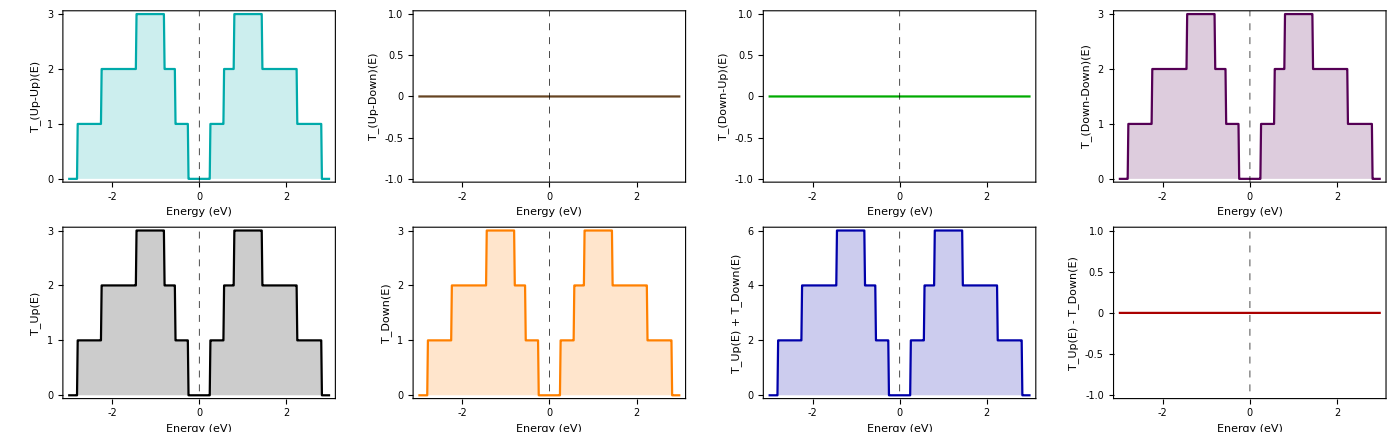

```mathematica
(******************************************* System Parameters ************************************************)
h=0;r=1;
onsiteChannel={{h,0},{0,-h}}; tHorizontalChannel={{1,0},{0,1}}; tVerticalChannel = {{1,0},{0,1}};
τSC =1; τCD = τSC; 
tHS=1;tVS=tHS;
onsiteSource={{h,0},{0,-h}}; tHorizontalSource={{tHS,0},{0,tHS}}; tVerticalSource =tHorizontalSource;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,12}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian =ArrayFlatten[ Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource =ArrayFlatten[ Table[If[Hamiltonian[[r,c+2  Max[surfaceElements1]]]==0,0,τSC],{r,2*Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source=ArrayFlatten[Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,tHS],{r,2 *Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΓSUp=Table[If[OddQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
          ΓSDw=Table[If[EvenQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(2 Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
ΓDUp=Table[If[OddQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
	 ΓDDw=Table[If[EvenQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian];
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm];
Map[MatrixForm,{ΓSUp,ΓSDw,ΓDUp,ΓDDw}]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*Print[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]," ", Chop[Tr[ΓSUp.GR.ΓDDw.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDUp.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDDw.GA]]];*)
{E1, Chop[Tr[ΓSUp.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]],Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]+Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]-Chop[Tr[ΓSUp.GR.ΓDDw.GA]]-Chop[Tr[ΓSDw.GR.ΓDDw.GA]]]},{E1,-3.01,3.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
TUU = ListLinePlot[transmission[[All,{1,2}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Cyan]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUD = ListLinePlot[transmission[[All,{1,3}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Brown]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDU = ListLinePlot[transmission[[All,{1,4}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Green]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDD = ListLinePlot[transmission[[All,{1,5}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Purple]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TU = ListLinePlot[transmission[[All,{1,6}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TD = ListLinePlot[transmission[[All,{1,7}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Orange],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUPlusD = ListLinePlot[transmission[[All,{1,8}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Blue]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) + T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUMinusD = ListLinePlot[transmission[[All,{1,9}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Red]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) - T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
GraphicsGrid[{{TUU,TUD,TDU,TDD},{TU,TD,TUPlusD,TUMinusD}},Spacings->1,ImageSize->1400]
```

## 3D System (spin-less and spin-full)

### Model - 3D

```mathematica
(*Function to generate a supercell*)GenerateSupercell[atoms_,a1_,a2_,a3_,nx_,ny_,nz_]:=Module[{supercell},supercell=Flatten[Table[(#+n a1+m a2+p a3)&/@atoms,{n,0,nx-1},{m,0,ny-1},{p,0,nz-1}],3];
supercell];

(*Function to group atoms by distance*)
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Lattice and atom positions*)
atomPositions={{0,0,0}};(*Atoms in the unit cell*)ax={1,0,0};(*Lattice vector in x-direction*)ay={0,1,0};(*Lattice vector in y-direction*)az={0,0,1};(*Lattice vector in z-direction*)
nx=5;ny=3;nz=3;(*Number of unit cells in each direction*)(*Generate the supercell*)supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,az,nx,ny,nz],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Visualization of the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[supercellCoordinates[[i]],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],supercellCoordinates[[i]]]],{i,1,Length[supercellCoordinates]}],ViewPoint->{1,1,1},ImageSize->500]

(*Nearest neighbors*)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]},{point,latticeCoordinates}];

nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}];

NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates];
```

-Graphics3D-

### Transmission (Spin-less)

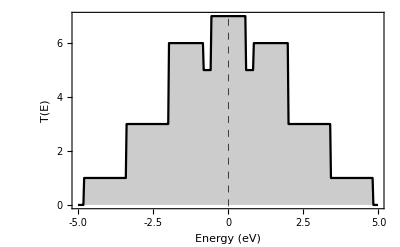

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,9}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-5.01,5.01,0.0257}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

### Transmission (Spin-full)

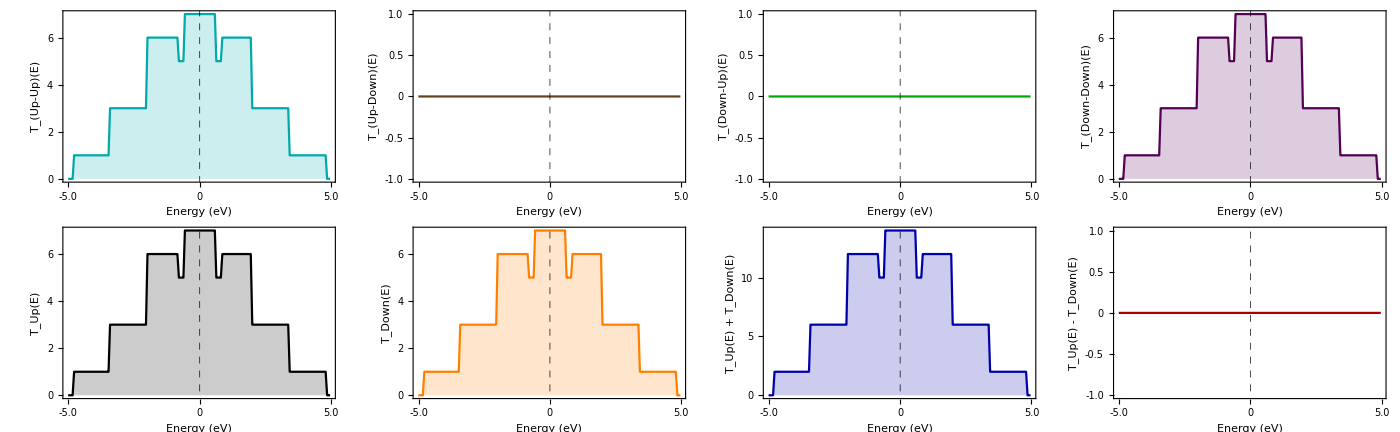

```mathematica
(******************************************* System Parameters ************************************************)
h=0;r=1;
onsiteChannel={{h,0},{0,-h}}; tHorizontalChannel={{1,0},{0,1}}; tVerticalChannel = {{1,0},{0,1}};
τSC =1; τCD = τSC; 
tHS=1;tVS=tHS;
onsiteSource={{h,0},{0,-h}}; tHorizontalSource={{tHS,0},{0,tHS}}; tVerticalSource =tHorizontalSource;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,9}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian =ArrayFlatten[ Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource =ArrayFlatten[ Table[If[Hamiltonian[[r,c+2  Max[surfaceElements1]]]==0,0,τSC],{r,2*Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source=ArrayFlatten[Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,tHS],{r,2 *Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΓSUp=Table[If[OddQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
          ΓSDw=Table[If[EvenQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(2 Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
ΓDUp=Table[If[OddQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
	 ΓDDw=Table[If[EvenQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian];
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm];
Map[MatrixForm,{ΓSUp,ΓSDw,ΓDUp,ΓDDw}]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*Print[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]," ", Chop[Tr[ΓSUp.GR.ΓDDw.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDUp.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDDw.GA]]];*)
{E1, Chop[Tr[ΓSUp.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]],Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]+Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]-Chop[Tr[ΓSUp.GR.ΓDDw.GA]]-Chop[Tr[ΓSDw.GR.ΓDDw.GA]]]},{E1,-5.01,5.01,0.057}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
TUU = ListLinePlot[transmission[[All,{1,2}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Cyan]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUD = ListLinePlot[transmission[[All,{1,3}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Brown]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDU = ListLinePlot[transmission[[All,{1,4}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Green]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDD = ListLinePlot[transmission[[All,{1,5}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Purple]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TU = ListLinePlot[transmission[[All,{1,6}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TD = ListLinePlot[transmission[[All,{1,7}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Orange],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUPlusD = ListLinePlot[transmission[[All,{1,8}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Blue]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) + T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUMinusD = ListLinePlot[transmission[[All,{1,9}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Red]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) - T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
GraphicsGrid[{{TUU,TUD,TDU,TDD},{TU,TD,TUPlusD,TUMinusD}},Spacings->1,ImageSize->1400]
```

## V3 :: 1, 2 and 4 atom Square lattice - using hopping generated from geometry - solve Dyson Iteratively (G = g + g v g ...) (X)

### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{0,0}(*,{0,1},{1,0},{1,1}*)};
ax = {1,0};
ay = {0,1};
nx=5; ny=1;
supercellCoordinates=latticeCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2}},{2,{1,3}},{3,{2,4}},{4,{3,5}},{5,{4}}}

### Transmission

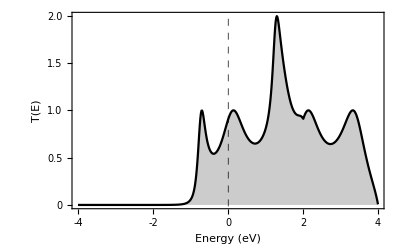

10 10 10 10 10

(-0.188152-0.184752 ⅈ | 0.0251802+0.184751 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0.0251802+0.184751 ⅈ | -0.188152-0.184752 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | -0.188152-0.184752 ⅈ | 0.0251802+0.184751 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.0251802+0.184751 ⅈ | -0.188152-0.184752 ⅈ)(0.369503 | -0.369502 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
-0.369502 | 0.369503 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0.369503 | -0.369502
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | -0.369502 | 0.369503)

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=2; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = .8; τCD = τSC; 
onsiteSource=1; tHorizontalSource=1.; tVerticalSource = 1.5;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;r=1;
surfaceElements1=Sort@Table[i,{i,1,4}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]
```

```mathematica
Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]
```

0 0 0 0 10

ΣSΣDΓSΓD

### Transmission (still have to try)

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=-1; tVerticalChannel =- 1;
τSC = -1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=-1.; tVerticalSource =- 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,1}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;



Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}]

E1=.51;
(******************************************* Self energy for Source ************************************************)
tolerance=0.001;
maxIterations=3;
iteration=0;
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; 
gS11//MatrixForm
GS11initial = gS11;
gSmidI =  gS11;
While[True,iteration++;
gSmidF=gS11.τ0Source.gSmidI;
Print[gSmidF];
GS11 = GS11initial + gSmidF;
If[Abs[GS11-GS11initial]<tolerance || iteration > maxIterations,Break[];];
gSmidI = gSmidF;
GS11initial = GS11;
]
GS11//MatrixForm
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].GS11.τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΣD =ΣS;
ΓD =ΓS ;
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
Chop[ Tr[ΓS.GR.ΓD.GA]]
(*E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];*)
```

{(0 | -1 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0
0 | -1 | 0 | -1 | 0
0 | 0 | -1 | 0 | -1
0 | 0 | 0 | -1 | 0),(-1),(0),(-1.)}

(1.96078-0.0000384468 ⅈ)

{{-3.84468+0.000150772 ⅈ}}

{{7.53858-0.000443446 ⅈ}}

{{-14.7815+0.00115934 ⅈ}}

{{28.9834-0.00284151 ⅈ}}

(19.8565-0.00201329 ⅈ)

1.24308×10^-8

```mathematica
Abs[GS11-GS11initial]
```

{{28.9834}}

```mathematica
gS11
```

{{1.96078-0.0000384468 ⅈ}}

```mathematica
1/(.5+ⅈ 0.0000001)
```

2.-4.×10^-7 ⅈ

```mathematica
Hamiltonian
```

```mathematica
alphaSource={{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}};
τSource=τ0Source={{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{1,0,0,0,0}};

E1=.51;
(******************************************* Self energy for Source ************************************************)
tolerance=0.001;
maxIterations=3;
iteration=0;
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; 
gS11//MatrixForm
GS11initial = gS11;
gSmidI =  gS11;
While[True,iteration++;
gSmidF=gS11.τ0Source.gSmidI;
Print[gSmidF];
GS11 = GS11initial + gSmidF;
If[Abs[GS11-GS11initial]<tolerance || iteration > maxIterations,Break[];];
gSmidI = gSmidF;
GS11initial = GS11;
]
GS11//MatrixForm
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].GS11.τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΣD =ΣS;
ΓD =ΓS ;
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
Chop[ Tr[ΓS.GR.ΓD.GA]]
```

(1.96078-0.0000384468 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.96078-0.0000384468 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 1.96078-0.0000384468 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.96078-0.0000384468 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.96078-0.0000384468 ⅈ)

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{3.84468-0.000150772 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

(1.96078-0.0000384468 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.96078-0.0000384468 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 1.96078-0.0000384468 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.96078-0.0000384468 ⅈ | 0.+0. ⅈ
3.84468-0.000150772 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.96078-0.0000384468 ⅈ)

Thread::tdlen: Objects of unequal length in … cannot be combined.

Thread::tdlen: Objects of unequal length in {{0,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{0,0,0,1,0}}+{{0.51,0,0,0,0},{0,0.51,0,0,0},{0,0,0.51,0,0},{0,0,0,0.51,0},{0,0,0,0,0.51}}+{{-3.92157+0.0000768935 ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}} cannot be combined.

Tr[{{0.0000768935,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.Inverse[{{0,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{0,0,0,1,0}}+{{0.51,0,0,0,0},{0,0.51,0,0,0},{0,0,0.51,0,0},{0,0,0,0.51,0},{0,0,0,0,0.51}}+{{-3.92157+0.0000768935 ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}].{{0.0000768935,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.ConjugateTranspose[Inverse[{{0,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{0,0,0,1,0}}+{{0.51,0,0,0,0},{0,0.51,0,0,0},{0,0,0.51,0,0},{0,0,0,0.51,0},{0,0,0,0,0.51}}+{{-3.92157+0.0000768935 ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}]]]

## Lieb Lattice - Altermagnet (initial code with no sublattice and 2nd NNH info can be checked for all higher hopping equals to 1 or same value 1NNH == 2NNH==3NNH)

### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{0,0},{0,1},{1,0}};
ax = {2,0};
ay = {0,2};
nx=3; ny=3;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
maxY=Max[supercellCoordinates[[All,2]]];
supercellCoordinates= supercellCoordinates=Select[supercellCoordinates,#[[2]]<maxY&];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.0,1.5]; (*To plot the bonds NNH1 or NNH2*)

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.5&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.5&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,6}},{2,{1,3,6,7}},{3,{2,4,7}},{4,{3,5,7,8}},{5,{4,8}},{6,{1,2,9,10}},{7,{2,3,4,10,11,12}},{8,{4,5,12,13}},{9,{6,10,14}},{10,{6,7,9,11,14,15}},{11,{7,10,12,15}},{12,{7,8,11,13,15,16}},{13,{8,12,16}},{14,{9,10,17,18}},{15,{10,11,12,18,19,20}},{16,{12,13,20,21}},{17,{14,18,22}},{18,{14,15,17,19,22,23}},{19,{15,18,20,23}},{20,{15,16,19,21,23,24}},{21,{16,20,24}},{22,{17,18}},{23,{18,19,20}},{24,{20,21}}}

### Transmission

{(0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 1. | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 1. | 0 | 0 | 0),(0 | 1. | 0 | 0 | 0 | 1. | 0 | 0
1. | 0 | 1. | 0 | 0 | 1. | 1. | 0
0 | 1. | 0 | 1. | 0 | 0 | 1. | 0
0 | 0 | 1. | 0 | 1. | 0 | 1. | 1.
0 | 0 | 0 | 1. | 0 | 0 | 0 | 1.
1. | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 1. | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 1. | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 1. | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 1. | 0 | 0 | 0)}

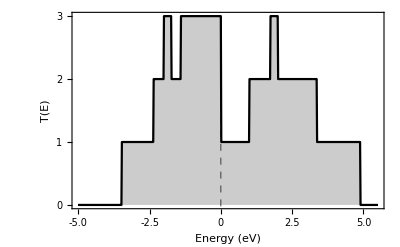

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1.; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@supercellCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}]

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-5.01,5.51,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

## Lieb Lattice with sub-lattice info - Altermagnet (Spin-less)

### Model

```mathematica
(******************************************Function to generate a supercell with hoppings ******************************************)GenerateSupercell[atoms_,sublattices_,a1_,a2_,nx_,ny_]:=Module[{supercell,sublatticeInfo},
supercell=Flatten[Table[Transpose[{(#+n a1+m a2)&/@atoms,sublattices}],{n,0,nx-1},{m,0,ny-1}],2];
sublatticeInfo=SortBy[supercell,First];sublatticeInfo];

GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},
pairs=Select[Subsets[coordinates,{2}],minDist<=EuclideanDistance[#[[1,1]],#[[2,1]]]<=maxDist&];
pairs];

(******************************************Generate a NxN supercell and Plot*****************************************)
atomPositions={{0,0},{0,1},{1,0}};
sublattices={"A","B","C"};
ax={2,0};
ay={0,2};
nx=3;ny=3;
minDistance=0.5; maxDistance=1.5;

supercellCoordinates=GenerateSupercell[atomPositions,sublattices,ax,ay,nx,ny];
(*maxY=Max[supercellCoordinates[[All,1,2]]]; (*Filter out atoms based on a maximum y-condition if needed*)
supercellCoordinates=Select[supercellCoordinates,#[[1,2]]<maxY&];*)
hoppings=GroupAtomsByDistance[supercellCoordinates,minDistance,maxDistance]; (*Generate hoppings considering sublattice information*)

(******************************************Plot the structure******************************************)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i,1]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.,0.52,0.66],Specularity[White,20],Opacity[0.5],Cylinder[Append[#,0]&/@hoppings[[i,All,1]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[Row[{i,", ",supercellCoordinates[[i,2]]}],17,Black,Bold],Append[supercellCoordinates[[i,1]],0]+{0.3,0.23,0}]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(*******************************nearest neighbors*******************************)
nearestNeighbors[supercell_,minDist_, maxDist_]:=Table[{supercell[[i,1]],supercell[[i,2]],Select[supercell,minDist<=EuclideanDistance[#[[1]],supercell[[i,1]]]<=maxDist&][[All,{1,2}]] },{i,Length[supercell]}]

nearestNeighborsIndex[supercell_,minDist_, maxDist_]:=Table[{i,supercell[[i,2]],Flatten[First@Position[supercell[[All,1]],#[[1]]]&/@Select[supercell,minDist<=EuclideanDistance[#[[1]],supercell[[i,1]]]<=maxDist&]] },{i,Length[supercell]}]


NNH=nearestNeighbors[supercellCoordinates, minDistance , maxDistance];
NNHI=nearestNeighborsIndex[supercellCoordinates, minDistance , maxDistance];
```

-Graphics3D-

### Hamiltonian

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; t1Channel=t1C; t2Channel = t2C;
τ1SC = 1; τ2SC =- .5;
τ1CD = τ1SC; τ2CD = τ2SC;
onsiteSource=0; t1Source=t1S; t2Source =t2S;
onsiteDrain=onsiteSource; t1Drain=t1Source; t2Drain = t2Source ;
nnh1Dist = 1.1; nnh2Dist = 1.5;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,6}];

(****************************************** system hamiltonian with higher NNH ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@supercellCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Channel,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Channel,0]]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,If[Hamiltonian[[r,c+Max[surfaceElements1]]]==t1Channel,τ1SC,τ2SC]],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Source,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Source,0]]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source= Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,If[Hamiltonian[[r,c+Max[surfaceElements1]]]==t1Channel,t1Source,t2Source]],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian, τSource, alphaSource, τ0Source }]
```

{(0 | t1C | 0 | 0 | t1C | 0 | 0 | 0 | 0 | 0 | 0 | 0
t1C | 0 | t1C | 0 | t2C | t2C | 0 | 0 | 0 | 0 | 0 | 0
0 | t1C | 0 | t1C | 0 | t1C | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t1C | 0 | 0 | t2C | 0 | 0 | 0 | 0 | 0 | 0
t1C | t2C | 0 | 0 | 0 | 0 | t1C | t2C | 0 | 0 | 0 | 0
0 | t2C | t1C | t2C | 0 | 0 | 0 | t2C | t1C | t2C | 0 | 0
0 | 0 | 0 | 0 | t1C | 0 | 0 | t1C | 0 | 0 | t1C | 0
0 | 0 | 0 | 0 | t2C | t2C | t1C | 0 | t1C | 0 | t2C | t2C
0 | 0 | 0 | 0 | 0 | t1C | 0 | t1C | 0 | t1C | 0 | t1C
0 | 0 | 0 | 0 | 0 | t2C | 0 | 0 | t1C | 0 | 0 | t2C
0 | 0 | 0 | 0 | 0 | 0 | t1C | t2C | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | t2C | t1C | t2C | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1 | If[t2C==t1C,τ1SC,τ2SC] | 0 | 0 | 0 | 0
0 | If[t2C==t1C,τ1SC,τ2SC] | 1 | If[t2C==t1C,τ1SC,τ2SC] | 0 | 0),(0 | t1S | 0 | 0 | t1S | 0
t1S | 0 | t1S | 0 | t2S | t2S
0 | t1S | 0 | t1S | 0 | t1S
0 | 0 | t1S | 0 | 0 | t2S
t1S | t2S | 0 | 0 | 0 | 0
0 | t2S | t1S | t2S | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
t1S | If[t2C==t1C,t1Source,t2Source] | 0 | 0 | 0 | 0
0 | If[t2C==t1C,t1Source,t2Source] | t1S | If[t2C==t1C,t1Source,t2Source] | 0 | 0)}

### Hamiltonian , Eigenvalues and Density of states

System size = 768

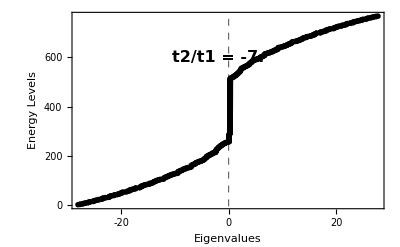
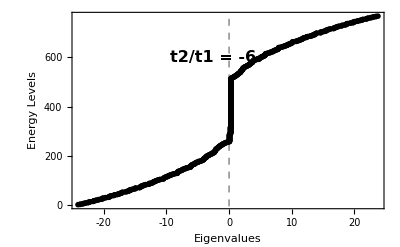
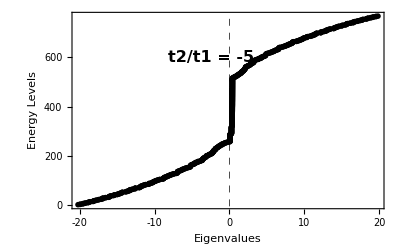
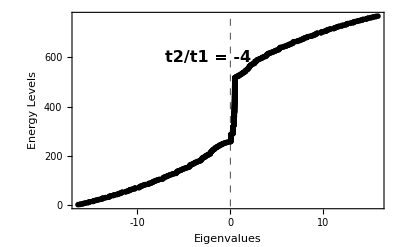
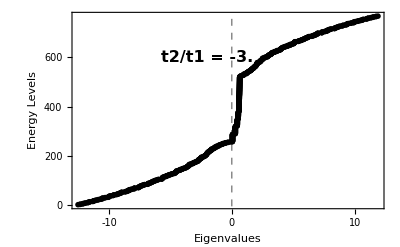
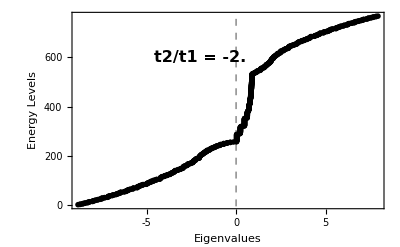
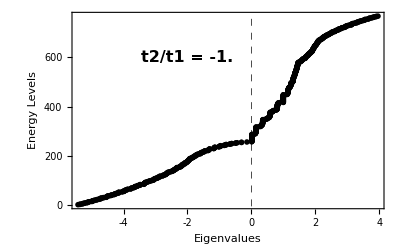
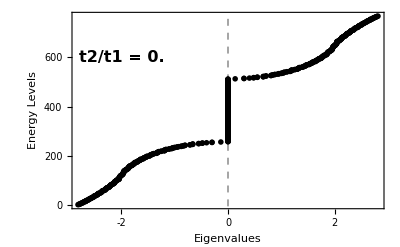

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; t1Channel=1.; t2Channel =.;
τ1SC = 1; τ2SC =-.5;
τ1CD = τ1SC; τ2CD = τ2SC;
onsiteSource=0; t1Source=t1S; t2Source =t2S;
onsiteDrain=onsiteSource; t1Drain=t1Source; t2Drain = t2Source ;
nnh1Dist = 1.1; nnh2Dist = 1.5;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,6}];

(****************************************** system hamiltonian with higher NNH ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@supercellCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Channel,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Channel,0]]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(****************************************** Eigen-value plot********************************)
Print["System size = ", Length@Hamiltonian]
ParallelTable[evals1=N@Eigenvalues[Hamiltonian]//Sort;
evals=Table[{evals1[[i]],i},{i,1,Length@evals1}];
tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
eplot=ListPlot[evals,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black],PointSize[0.01]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Eigenvalues",20],Style["Energy Levels ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,GridLines->{{0},{}},GridLinesStyle->Directive[Black,Dashed],Epilog->{Text[Style["t2/t1 = "<>ToString[t2Channel/t1Channel],FontSize->16,Bold],{-2,600}]}],{t2Channel,-7,7,1}]
```

### Hamiltonian and Trnasmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

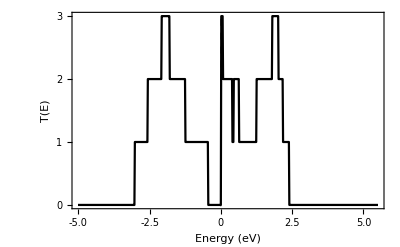

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; t1Channel=1; t2Channel = -t1Channel/(√2)^5;
τ1SC = 1; τ2SC =t2Channel;
τ1CD = τ1SC; τ2CD = τ2SC;
onsiteSource=0; t1Source=1.; t2Source =t2Channel;
onsiteDrain=onsiteSource; t1Drain=t1Source; t2Drain = t2Source ;
nnh1Dist = 1.1; nnh2Dist = 1.5;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,9}];

(****************************************** system hamiltonian with higher NNH ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@supercellCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Channel,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Channel,0]]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,If[Hamiltonian[[r,c+Max[surfaceElements1]]]==t1Channel,τ1SC,τ2SC]],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Source,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Source,0]]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source= Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,If[Hamiltonian[[r,c+Max[surfaceElements1]]]==t1Channel,t1Source,t2Source]],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian, τSource, alphaSource, τ0Source }];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-5.01,5.51,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,(*Filling->Axis,*)GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

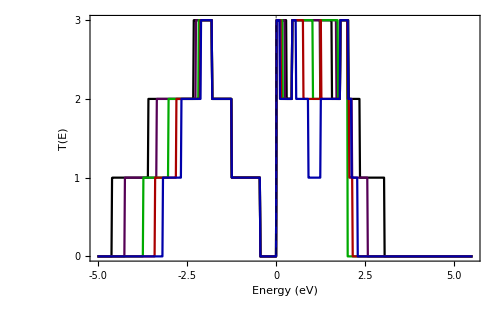

```mathematica
Show[%2838,%2668,%2711,%2754,%2797,ImageSize->500]
```

## Lieb Lattice with sub-lattice info - Altermagnet (Spin-Full)

### Model

```mathematica
(******************************************Function to generate a supercell with hoppings ******************************************)GenerateSupercell[atoms_,sublattices_,a1_,a2_,nx_,ny_]:=Module[{supercell,sublatticeInfo},
supercell=Flatten[Table[Transpose[{(#+n a1+m a2)&/@atoms,sublattices}],{n,0,nx-1},{m,0,ny-1}],2];
sublatticeInfo=SortBy[supercell,First];sublatticeInfo];

GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},
pairs=Select[Subsets[coordinates,{2}],minDist<=EuclideanDistance[#[[1,1]],#[[2,1]]]<=maxDist&];
pairs];

(******************************************Generate a NxN supercell and Plot*****************************************)
atomPositions={{0,0},{0,1},{1,0}};
sublattices={"A","B","C"};
ax={2,0};
ay={0,2};
nx=2;ny=2;
minDistance=0.5; maxDistance=1.5;

supercellCoordinates=GenerateSupercell[atomPositions,sublattices,ax,ay,nx,ny];
(*maxY=Max[supercellCoordinates[[All,1,2]]]; (*Filter out atoms based on a maximum y-condition if needed*)
supercellCoordinates=Select[supercellCoordinates,#[[1,2]]<maxY&];*)
hoppings=GroupAtomsByDistance[supercellCoordinates,minDistance,maxDistance]; (*Generate hoppings considering sublattice information*)

(******************************************Plot the structure******************************************)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i,1]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,All,1]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[Row[{i,", ",supercellCoordinates[[i,2]]}],16,Black,Bold],Append[supercellCoordinates[[i,1]],0]+{0.4,0.3,0}]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(*******************************nearest neighbors*******************************)
nearestNeighbors[supercell_,minDist_, maxDist_]:=Table[{supercell[[i,1]],supercell[[i,2]],Select[supercell,minDist<=EuclideanDistance[#[[1]],supercell[[i,1]]]<=maxDist&][[All,{1,2}]] },{i,Length[supercell]}]

nearestNeighborsIndex[supercell_,minDist_, maxDist_]:=Table[{i,supercell[[i,2]],Flatten[First@Position[supercell[[All,1]],#[[1]]]&/@Select[supercell,minDist<=EuclideanDistance[#[[1]],supercell[[i,1]]]<=maxDist&]] },{i,Length[supercell]}]


NNH=nearestNeighbors[supercellCoordinates, minDistance , maxDistance];
NNHI=nearestNeighborsIndex[supercellCoordinates, minDistance , maxDistance]
```

-Graphics3D-

{{1,A,{2,5}},{2,B,{1,3,5,6}},{3,A,{2,4,6}},{4,B,{3,6}},{5,C,{1,2,7,8}},{6,C,{2,3,4,8,9,10}},{7,A,{5,8,11}},{8,B,{5,6,7,9,11,12}},{9,A,{6,8,10,12}},{10,B,{6,9,12}},{11,C,{7,8}},{12,C,{8,9,10}}}

### Model

```mathematica
(******************************************Function to generate a supercell with hoppings ******************************************)GenerateSupercell[atoms_,sublattices_,a1_,a2_,nx_,ny_]:=Module[{supercell,sublatticeInfo},
supercell=Flatten[Table[Transpose[{(#+n a1+m a2)&/@atoms,sublattices}],{n,0,nx-1},{m,0,ny-1}],2];
sublatticeInfo=SortBy[supercell,First];sublatticeInfo];

GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},
pairs=Select[Subsets[coordinates,{2}],minDist<=EuclideanDistance[#[[1,1]],#[[2,1]]]<=maxDist&];
pairs];

(******************************************Generate a NxN supercell and Plot*****************************************)
atomPositions={{0,0},{0,1},{1,0}};
sublattices={"A","B","C"};
ax={2,0};
ay={0,2};
nx=3;ny=4;
minDistance=0.5; maxDistance=1.5;

supercellCoordinates=GenerateSupercell[atomPositions,sublattices,ax,ay,nx,ny];
(*maxY=Max[supercellCoordinates[[All,1,2]]]; (*Filter out atoms based on a maximum y-condition if needed*)
supercellCoordinates=Select[supercellCoordinates,#[[1,2]]<maxY&];*)
hoppings=GroupAtomsByDistance[supercellCoordinates,minDistance,maxDistance]; (*Generate hoppings considering sublattice information*)

(******************************************Plot the structure******************************************)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i,1]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.,0.52,0.66],Specularity[White,20],Opacity[0.5],Cylinder[Append[#,0]&/@hoppings[[i,All,1]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[Row[{i,", ",supercellCoordinates[[i,2]]}],17,Black,Bold],Append[supercellCoordinates[[i,1]],0]+{0.3,0.23,0}]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(*******************************nearest neighbors*******************************)
nearestNeighbors[supercell_,minDist_, maxDist_]:=Table[{supercell[[i,1]],supercell[[i,2]],Select[supercell,minDist<=EuclideanDistance[#[[1]],supercell[[i,1]]]<=maxDist&][[All,{1,2}]] },{i,Length[supercell]}]

nearestNeighborsIndex[supercell_,minDist_, maxDist_]:=Table[{i,supercell[[i,2]],Flatten[First@Position[supercell[[All,1]],#[[1]]]&/@Select[supercell,minDist<=EuclideanDistance[#[[1]],supercell[[i,1]]]<=maxDist&]] },{i,Length[supercell]}]


NNH=nearestNeighbors[supercellCoordinates, minDistance , maxDistance];
NNHI=nearestNeighborsIndex[supercellCoordinates, minDistance , maxDistance];
```

-Graphics3D-

### Hamiltonian

```mathematica
(******************************************* System Parameters ************************************************)
hc=h;t1c=.;t2c=.;r=1;
ϵcA={{0,0},{0,0}};ϵcB={{hc,0},{0,-hc}};ϵcC={{-hc,0},{0,hc}};
onsiteChannel={{0,0},{0,0}}; t1Channel={{t1c,0},{0,t1c}}; t2Channel = {{t2c,0},{0,t2c}};

τ1SC = 1; τ2SC =-.5;
τ1CD = τ1SC; τ2CD = τ2SC;

hs=1; t1s=1; t2s = -.5;
ϵsA={{0,0},{0,0}};ϵsB={{hs,0},{0,-hs}};ϵsC={{-hs,0},{0,hs}};
onsiteSource={{0,0},{0,0}}; t1Source={{t1s,0},{0,t1s}}; t2Source ={{t2s,0},{0,t2s}};
onsiteDrain=onsiteSource; t1Drain=t1Source; t2Drain = t2Source ;

nnh1Dist = 1.1; nnh2Dist = 1.5;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,6}];

(****************************************** system hamiltonian with higher NNH ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@supercellCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = ArrayFlatten[ Table[If[r==c ,If[NNHI[[r,2]]=="A",ϵcA,If[NNHI[[r,2]]=="B",ϵcB,If[NNHI[[r,2]]=="C",ϵcC,onsiteChannel]]],If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Channel,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Channel,0]]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource = ArrayFlatten[ Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,If[Hamiltonian[[r,c+2 Max[surfaceElements1]]]==t1c,τ1SC,τ2SC]],{r,2 Length@surfaceElements1},{c,2 Length@surfaceElements1}]]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[ Table[If[r==c,If[NNHI[[r,2]]=="A",ϵsA,If[NNHI[[r,2]]=="B",ϵsB,If[NNHI[[r,2]]=="C",ϵsC,onsiteSource]]],If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Source,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Source,0]]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source= ArrayFlatten[ Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,If[Hamiltonian[[r,c+2 Max[surfaceElements1]]]==t1c,t1s,t2s]],{r,2  Length@surfaceElements1},{c,2  Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian, τSource, alphaSource, τ0Source }]
```

{(0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
t1c | 0 | h | 0 | t1c | 0 | 0 | 0 | t2c | 0 | t2c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t1c | 0 | -h | 0 | t1c | 0 | 0 | 0 | t2c | 0 | t2c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t1c | 0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | t1c | 0 | h | 0 | 0 | 0 | t2c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t1c | 0 | -h | 0 | 0 | 0 | t2c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
t1c | 0 | t2c | 0 | 0 | 0 | 0 | 0 | -h | 0 | 0 | 0 | t1c | 0 | t2c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t1c | 0 | t2c | 0 | 0 | 0 | 0 | 0 | h | 0 | 0 | 0 | t1c | 0 | t2c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t2c | 0 | t1c | 0 | t2c | 0 | 0 | 0 | -h | 0 | 0 | 0 | t2c | 0 | t1c | 0 | t2c | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t2c | 0 | t1c | 0 | t2c | 0 | 0 | 0 | h | 0 | 0 | 0 | t2c | 0 | t1c | 0 | t2c | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2c | 0 | t2c | 0 | t1c | 0 | h | 0 | t1c | 0 | 0 | 0 | t2c | 0 | t2c | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2c | 0 | t2c | 0 | t1c | 0 | -h | 0 | t1c | 0 | 0 | 0 | t2c | 0 | t2c
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c | 0 | 0 | 0 | t1c
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2c | 0 | 0 | 0 | 0 | 0 | t1c | 0 | h | 0 | 0 | 0 | t2c | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2c | 0 | 0 | 0 | 0 | 0 | t1c | 0 | -h | 0 | 0 | 0 | t2c
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t1c | 0 | t2c | 0 | 0 | 0 | 0 | 0 | -h | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t1c | 0 | t2c | 0 | 0 | 0 | 0 | 0 | h | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2c | 0 | t1c | 0 | t2c | 0 | 0 | 0 | -h | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t2c | 0 | t1c | 0 | t2c | 0 | 0 | 0 | h),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | If[t2c==t1c,τ1SC,τ2SC] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | If[t2c==t1c,τ1SC,τ2SC] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | If[t2c==t1c,τ1SC,τ2SC] | 0 | 1 | 0 | If[t2c==t1c,τ1SC,τ2SC] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | If[t2c==t1c,τ1SC,τ2SC] | 0 | 1 | 0 | If[t2c==t1c,τ1SC,τ2SC] | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -0.5 | 0 | -0.5 | 0
0 | 1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | -0.5 | 0 | -0.5
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -0.5 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -0.5
1 | 0 | -0.5 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 0 | -0.5 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -0.5 | 0 | 1 | 0 | -0.5 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -0.5 | 0 | 1 | 0 | -0.5 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | If[t2c==t1c,t1s,t2s] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | If[t2c==t1c,t1s,t2s] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | If[t2c==t1c,t1s,t2s] | 0 | 1 | 0 | If[t2c==t1c,t1s,t2s] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | If[t2c==t1c,t1s,t2s] | 0 | 1 | 0 | If[t2c==t1c,t1s,t2s] | 0 | 0 | 0 | 0)}

### Hamiltonian and Trnasmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

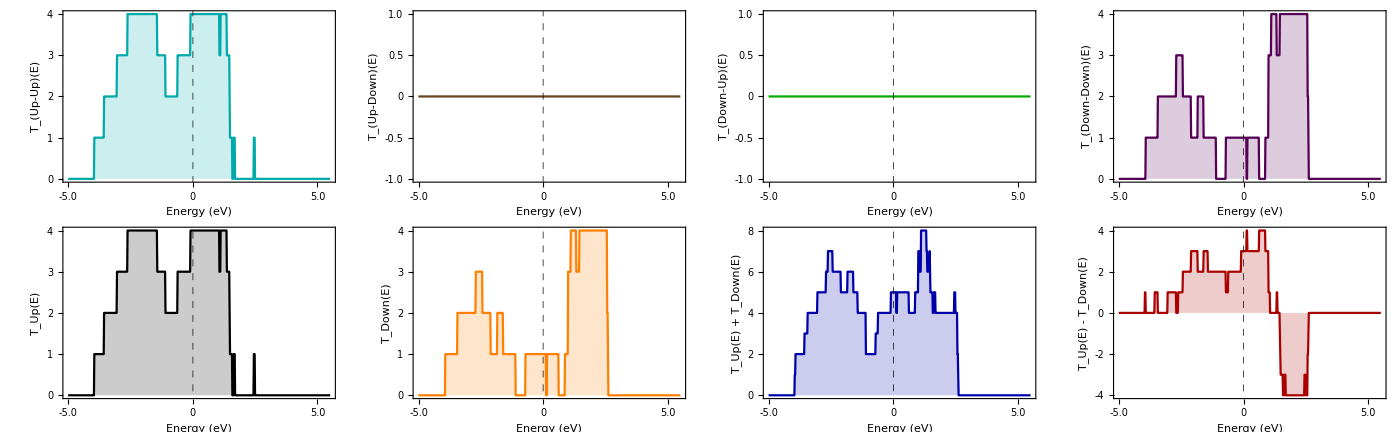

```mathematica
(******************************************* System Parameters ************************************************)
hc=1;t1c=1;t2c=-.5;r=1;
ϵcA={{0,0},{0,0}};ϵcB={{hc,0},{0,-hc}};ϵcC={{-hc,0},{0,hc}};
onsiteChannel={{0,0},{0,0}}; t1Channel={{t1c,0},{0,t1c}}; t2Channel = {{t2c,0},{0,t2c}};

τ1SC = 1; τ2SC =-.5;
τ1CD = τ1SC; τ2CD = τ2SC;

hs=1; t1s=1; t2s = -.5;
ϵsA={{0,0},{0,0}};ϵsB={{hs,0},{0,-hs}};ϵsC={{-hs,0},{0,hs}};
onsiteSource={{0,0},{0,0}}; t1Source={{t1s,0},{0,t1s}}; t2Source ={{t2s,0},{0,t2s}};
onsiteDrain=onsiteSource; t1Drain=t1Source; t2Drain = t2Source ;

nnh1Dist = 1.1; nnh2Dist = 1.5;
η=0.0001;
surfaceElements1=Sort@Table[i,{i,1,12}];

(****************************************** system hamiltonian with higher NNH ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@supercellCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = ArrayFlatten[ Table[If[r==c ,If[NNHI[[r,2]]=="A",ϵcA,If[NNHI[[r,2]]=="B",ϵcB,If[NNHI[[r,2]]=="C",ϵcC,onsiteChannel]]],If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Channel,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Channel,0]]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource = ArrayFlatten[ Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,If[Hamiltonian[[r,c+2 Max[surfaceElements1]]]==t1c,τ1SC,τ2SC]],{r,2 Length@surfaceElements1},{c,2 Length@surfaceElements1}]]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[ Table[If[r==c,If[NNHI[[r,2]]=="A",ϵsA,If[NNHI[[r,2]]=="B",ϵsB,If[NNHI[[r,2]]=="C",ϵsC,onsiteSource]]],If[MemberQ[NNHI[[r,3]],c] && EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh1Dist,t1Source,If[MemberQ[NNHI[[r,3]],c] && nnh1Dist<EuclideanDistance[supercellCoordinates[[r,1]],supercellCoordinates[[c,1]]]<= nnh2Dist,t2Source,0]]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source= ArrayFlatten[ Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,If[Hamiltonian[[r,c+2 Max[surfaceElements1]]]==t1c,t1s,t2s]],{r,2  Length@surfaceElements1},{c,2  Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian, τSource, alphaSource, τ0Source }];

E1=0;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΓSUp=Table[If[OddQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
          ΓSDw=Table[If[EvenQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(2 Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
ΓDUp=Table[If[OddQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
	 ΓDDw=Table[If[EvenQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian];
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm];
Map[MatrixForm,{ΓSUp,ΓSDw,ΓDUp,ΓDDw}]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*Print[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]," ", Chop[Tr[ΓSUp.GR.ΓDDw.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDUp.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDDw.GA]]];*)
{E1, Chop[Tr[ΓSUp.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]],Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]+Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]-Chop[Tr[ΓSUp.GR.ΓDDw.GA]]-Chop[Tr[ΓSDw.GR.ΓDDw.GA]]]},{E1,-5.01,5.51,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
TUU = ListLinePlot[transmission[[All,{1,2}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Cyan]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUD = ListLinePlot[transmission[[All,{1,3}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Brown]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDU = ListLinePlot[transmission[[All,{1,4}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Green]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDD = ListLinePlot[transmission[[All,{1,5}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Purple]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TU = ListLinePlot[transmission[[All,{1,6}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TD = ListLinePlot[transmission[[All,{1,7}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Orange],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUPlusD = ListLinePlot[transmission[[All,{1,8}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Blue]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) + T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUMinusD = ListLinePlot[transmission[[All,{1,9}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Red]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) - T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
GraphicsGrid[{{TUU,TUD,TDU,TDD},{TU,TD,TUPlusD,TUMinusD}},Spacings->1,ImageSize->1400]
```